```mathematica
<<Combinatorica`
<<GraphUtilities`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

MinimumVertexColoring::shdw: Symbol "MinimumVertexColoring" appears in multiple contexts {"Combinatorica`", "Global`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

ToCombinatoricaGraph::shdw: Symbol "ToCombinatoricaGraph" appears in multiple contexts {"GraphUtilities`", "Global`"}; definitions in context "GraphUtilities`" may shadow or be shadowed by other definitions.

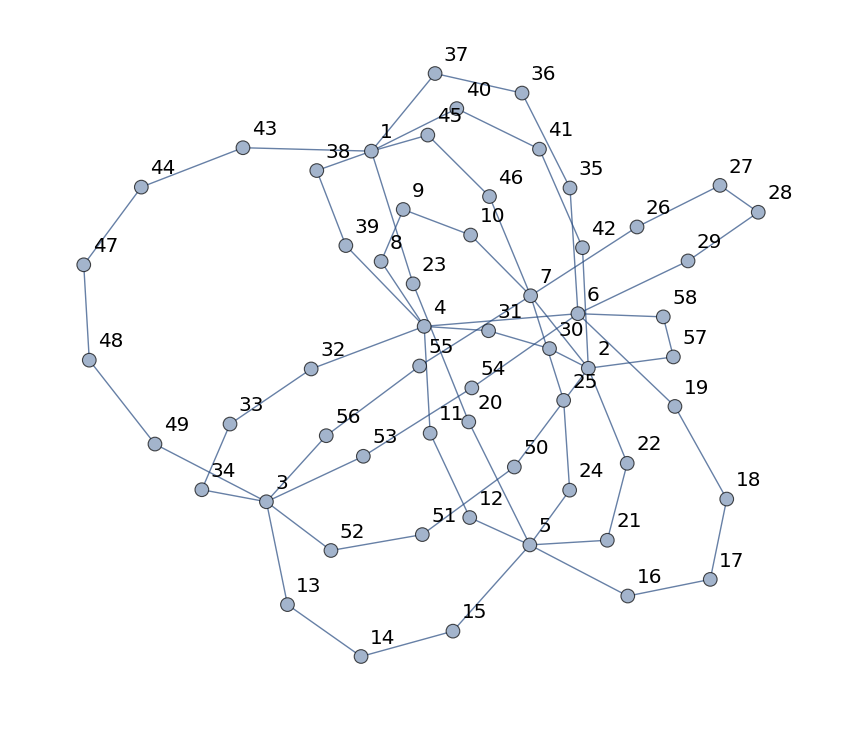

{1,2,2,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,1,1,1,2,1,1,2,1,2,1,2,1,2,1,1,1,2,1,1,2,1,1,3,1,3,1,3,3,1,3,2,1,2,1,2,3,1,2,1}

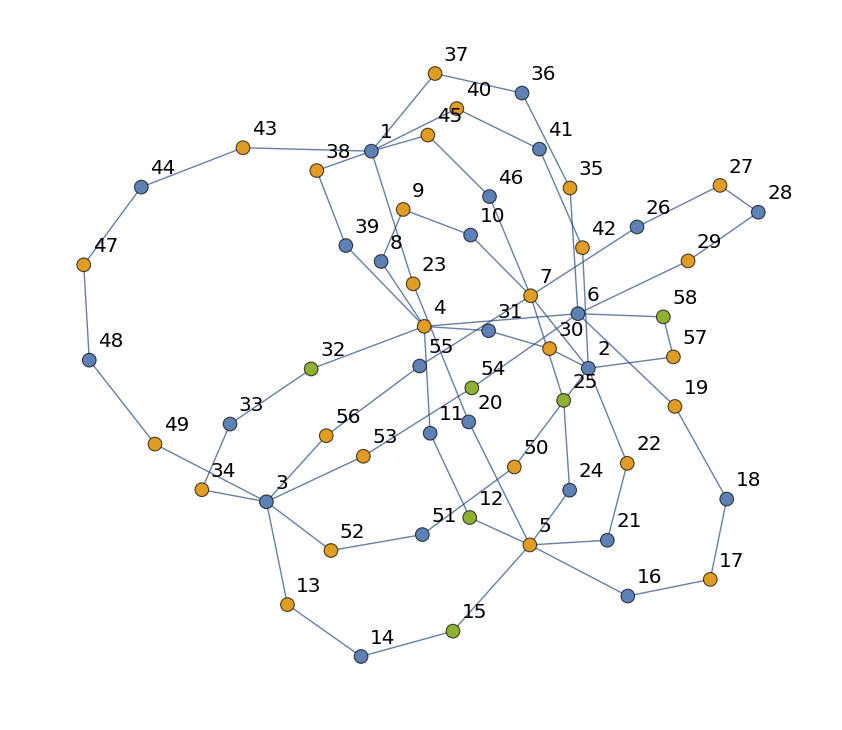

3

{1,40,43,38,23,37,45,2,50,30,22,57,7,3,34,13,53,56,4,11,6,8,5,16,24,29,41,42,44,47,48,49,39,20,36,35,46,51,52,31,21,58,33,32,14,15,54,55,12,9,10,17,18,19,25,28,27,26}

```mathematica
g=System`Graph[{1<->40,1<->43,1<->38,1<->23,1<->37,1<->45,2<->50,2<->30,2<->22,2<->57,2<->7,3<->34,3<->13,3<->53,3<->56,4<->11,4<->6,4<->8,5<->16,5<->24,6<->29,40<->41,41<->42,42<->2,43<->44,44<->47,47<->48,48<->49,49<->3,38<->39,39<->4,23<->20,20<->5,37<->36,36<->35,35<->6,45<->46,46<->7,50<->51,51<->52,52<->3,30<->31,31<->4,22<->21,21<->5,57<->58,58<->6,34<->33,33<->32,32<->4,13<->14,14<->15,15<->5,53<->54,54<->6,56<->55,55<->7,11<->12,12<->5,8<->9,9<->10,10<->7,16<->17,17<->18,18<->19,19<->6,24<->25,25<->7,29<->28,28<->27,27<->26,26<->7},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]

GColoredList=MinimumVertexColoring@ToCombinatoricaGraph[g]
GColored=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@GColoredList)]]
Max[GColoredList]
VertexList[GColored]
```